```mathematica
h = 6.626*10^(-34); (*J s*)
hbar = h/(2π);
e=-1.602*10^(-19); (* C *)
ϵ0=8.854*10^(-12); (* C^2/(J m) *)
me=9.109*10^(-31); (*kg*)
mp=1.673*10^(-27); (*kg*)
μ=(mp/(me+mp))*me;
a0=(4π ϵ0 hbar^2)/(μ e^2);
```

```mathematica
Ens=Table[-hbar^2/(a0^2 2 μ n^2)*1/(1.602*10^(-19)),{n,1,10}]
```

{-13.5941,-3.39852,-1.51045,-0.84963,-0.543763,-0.377613,-0.27743,-0.212408,-0.167828,-0.135941}

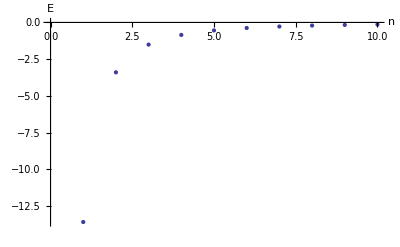

```mathematica
ListPlot[Ens, PlotRange->Full,AxesLabel->{"n", "E"}]
```